```mathematica
Copyright © 2021 Franz Utermohlen. All rights reserved.
```

Initialization cell

```mathematica
(*Clear all the definitions made during the current Wolfram System session*)
Clear["Global`*"];

(*Boltzmann's constant (units: meV/K)*)
kB=1000*8.617333262145*10^(-5);
(*meVs to K*)
meVtoK=1/kB;

(*====================================Spin wave Hamiltonian====================================*)

a=1;
γ=1;
(*Spin at each site*)
S=3/2;
nm=0;
(*Vectors*)
a1=Sqrt[3]a{1,0,0};
a2=(Sqrt[3]/2)a{1,Sqrt[3],0};
(*a3=a{0,0,1};*)
b1=2π/(3a){Sqrt[3],-1,0};
b2=4π/(3a){0,1,0};
(*b3=2π/a{0,0,1};*)
Γpoint={0,0,0};
Kpoint=4π/(3Sqrt[3]a){1,0,0};
Kprimepoint=(2 π)/(3a){1/Sqrt[3],1};
Mpoint=π/(3a){Sqrt[3],1,0};
δx=a/2{-Sqrt[3],-1,0};
δy=a/2{Sqrt[3],-1,0};
δz=a{0,1,0};
(*Ignore the e3-components of all of the vectors, since they are zero*)
{a1,a2,b1,b2,Γpoint,Kpoint,Mpoint,δx,δy,δz}=Most/@({a1,a2,b1,b2,Γpoint,Kpoint,Mpoint,δx,δy,δz});
(*Scalars*)
λ=-1/2(1+I Sqrt[3]);
Δ[kvec_]:=Exp[I kvec.δx]+Exp[I kvec.δy]+Exp[I kvec.δz];
ΔDM[kvec_]:=Sin[kvec.(δx-δy)]+Sin[kvec.(δy-δz)]+Sin[kvec.(δz-δx)];
ΔJ2[kvec_]:=Cos[kvec.(δx-δy)]+Cos[kvec.(δy-δz)]+Cos[kvec.(δz-δx)];
ΔJ3[kvec_]:=Exp[I kvec.(δx-δy+δz)]+Exp[I kvec.(δy-δz+δx)]+Exp[I kvec.(δz-δx+δy)];
d[kvec_]:=(3J+k+2Γ+2dSIA-2ΔDM[kvec]dDM+(6-2ΔJ2[kvec])J2+3J3)(nm-S)+γ H;
p[kvec_]:=S((1/3)(3J+k-Γ)Δ[kvec]+ΔJ3[kvec]J3);
q[kvec_]:=S/3(k+2Γ)(Conjugate[λ]Exp[I kvec.δx]+λ Exp[I kvec.δy]+Exp[I kvec.δz]);
η=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
(*Spin-wave Hamiltonian*)
h[kvec_]:=η.({{d[kvec], Conjugate[p[kvec]], 0, Conjugate[q[kvec]]}, {p[kvec], d[-kvec], Conjugate[q[-kvec]], 0}, {0, q[-kvec], d[-kvec], p[-kvec]}, {q[kvec], 0, Conjugate[p[-kvec]], d[kvec]}})/.{Conjugate[S]->S,Conjugate[J]->J,Conjugate[k]->k,Conjugate[Γ]->Γ,Conjugate[dSIA]->dSIA,Conjugate[dDM]->dDM,Conjugate[J2]->J2,Conjugate[J3]->J3,Conjugate[H]->H};

(*Number of magnon bands/modes in the energy spectrum (equivalently, the number of energy values per k-vector)*)
numMagnonBands=Length[
Select[
Chop[
Re[
N[
Eigenvalues[
h[{N[Sqrt[E]],N[Sqrt[EulerGamma]]}]/.{J->-1,k->-2,Γ->-3,dSIA->-5,dDM->7,J2->1/11,J3->1/13,H->1/17}
]
]
]
]
,#≥0&]
];

(*Eigenvalues*)
eigenvals[kvec_]:=
Sort[
Chop[
Re[
Eigenvalues[
h[kvec]
]
]
]
,Greater][[1;;numMagnonBands]];

(*Eigenvalues at the Γ point*)
eigenvalsΓpoint=FullSimplify[(*Re[*)Eigenvalues[h[Γpoint]](*]*),{J∈Reals,k∈Reals,Γ∈Reals,Γ<0,dDM∈Reals,dSIA∈Reals,J2∈Reals,J3∈Reals,H∈Reals}];
(*Eigenvalues at a K point*)
(*eigenvalsKpoint=FullSimplify[(*Re[*)Eigenvalues[h[Kpoint]](*]*),{J∈Reals,k∈Reals,Γ∈Reals,Γ<0,dDM∈Reals,dSIA∈Reals,J2∈Reals,J3∈Reals,H∈Reals}](*/.-1^(1/3)->-1*);*)
(*Eigenvalues at an M point*)
(*eigenvalsMpoint=FullSimplify[(*Re[*)Eigenvalues[h[Mpoint]](*]*),{J∈Reals,k∈Reals,Γ∈Reals,Γ<0,dDM∈Reals,dSIA∈Reals,J2∈Reals,J3∈Reals,H∈Reals}];*)

(*==============================================================================================*)

(*Procedure to obtain the k-space vectors for a given path in k-space*)
kvecsForPath[path_:{"Γ","M","K","Γ"},numSteps_:200]:=Module[{numLegs,point,displacementVectors,directionalVectors,distances,totDist,stepDist,numStepsList,stepIndex,kvecs},

(*Number of high symmetry points*)
numHighSymmetryPoints=Length[path];
(*Number of legs in the path;
Note: a leg is the part of the path from one high symmetry point point to the next; for example, the path K–Γ–M–K has 3 legs, namely K–Γ, Γ–M, and M–K*)
numLegs=numHighSymmetryPoints-1;
(*k-vector coordinate for each high symmetry point*)
point=Table[
If[path[[i]]=="Γ",
Γpoint
,(*else*)
If[path[[i]]=="K",
Kpoint
,(*else*)
If[path[[i]]=="K'",
Kprimepoint
,(*else*)
If[path[[i]]=="M",
Mpoint
]
]
]
]
,{i,1,numHighSymmetryPoints}];
(*List containing the displacement vector for each leg*)
displacementVectors=Table[point[[i+1]]-point[[i]],{i,1,numLegs}];
(*List containing directional (i.e., unit) vector for each displacement vector*)
directionalVectors=Normalize/@displacementVectors;
(*List containing the distance corresponding to each displacement vector (i.e., the length of each leg)*)
distances=Norm/@displacementVectors;
(*Total distance in k-space covered in our path*)
totDist=Total[distances];
(*Step distance in k-space*)
stepDist=totDist/numSteps;
(*List containing the number of steps corresponding to each leg*)
numStepsList=Table[Round[numSteps(distances[[i]]/totDist)],{i,1,numLegs}];
(*Check that they add to numSteps*)
(*Print[Total[numStepsList]==numSteps];*)
(*Lists containing the numbers corresponding to the first and last step of each leg*)
lastStep=Table[Total[numStepsList[[1;;i]]],{i,1,numLegs}];
firstStep=Join[{1},(lastStep[[1;;numLegs-1]]+1)];
(*Initialize the list containing the k vector for each step*)
kvecs=ConstantArray[0,numSteps+1];
(*Loop over all of the steps*)
stepIndex=0;
Do[
Do[
stepIndex+=1;

If[stepIndex==firstStep[[leg]],
kvecs[[stepIndex]]=point[[leg]];
,
kvecs[[stepIndex]]=kvecs[[stepIndex-1]]+stepDist directionalVectors[[leg]];
];

,{step,firstStep[[leg]],lastStep[[leg]]}];
,{leg,1,numLegs}];

(*Put in the last k point in by hand (corresponding to the last high symmetry point)*)
kvecs[[numSteps+1]]=point[[numHighSymmetryPoints]];

(*Check to see how far off we are at each of the high symmetry points*)
(*Do[
Print[
ToString[
N[Norm[kvecs[[firstStep[[i]]-1]]-point[[i]]]/stepDist]
]
<>
" steps"
];
,{i,2,numHighSymmetryPoints-1}]*)

(*Return kvecs*)
N[kvecs]

];

(*Procedure to the magnon band structure*)
plotMagnonBandStructure[path_:{"Γ","M","K","Γ"},ymin_:0,ymax_:Automatic,bandLinesStyle_:{Thickness[0.003],Red},highSymmetryPointsVerticalLinesStyle_:{Black,Dashed},yaxisLabelLeft_:"Energy / |J|",xaxisLabelBottom_:"Wavevector k",yaxisLabelRight_:None,xaxisLabelTop_:None,imageSize_:Large,numSteps_:200]:=Module[{kvecs,Emin,Emax,ΔE,yminLine,ymaxLine,highSymmetryPointsVerticalLines,ticks},

(*Obtain the k-space vectors for the path we are plotting*)
kvecs=kvecsForPath[path,numSteps];

data=Table[eigenvals[kvecs[[step]]],{step,1,numSteps+1}];

(*===Plot the magnon band structure===*)
Emin=Min[data];
Emax=Max[data];
ΔE=Emax-Emin;

yminLine=-5;
ymaxLine=100Emax;
highSymmetryPointsVerticalLines=Table[Line[{{firstStep[[i]],yminLine},{firstStep[[i]],ymaxLine}}],{i,2,numHighSymmetryPoints-1}];
ticks={{Automatic,Automatic},{Join[Table[{firstStep[[i]],path[[i]]},{i,1,numHighSymmetryPoints-1}],{{lastStep[[numHighSymmetryPoints-1]]+1,path[[numHighSymmetryPoints]]}}],None}};

(*Plot band structure*)
ListLinePlot[Transpose[data],
PlotRange->{{1,numSteps+1},{ymin,ymax}},
Frame->True,
(*Frame->{{True,False},{True,False}},*)
FrameLabel->{{yaxisLabelLeft,yaxisLabelRight},{xaxisLabelBottom,xaxisLabelTop}},
(*FrameLabel->{{"Energy (meV)",None},{"Wavevector k",None}},*)
FrameTicks->ticks,
PlotLabel->"Magnon band structure",
(*PlotLegends->SwatchLegend[{"E_+","E_-"}],*)
PlotStyle->Directive[bandLinesStyle],
LabelStyle->Directive[18,Black],
FrameStyle->Directive[18,Black],
Epilog->{Directive[highSymmetryPointsVerticalLinesStyle],highSymmetryPointsVerticalLines},
ImageSize->imageSize]

];

(*Procedure to plot path a k-space path (small plot version)*)
plotkspacePathSmall[path_:{"Γ","M","K","Γ"},numSteps_:200]:=Module[{kvecs,kvecsx,kvecsy,R,numCorners,corner,brillouinZoneEdges,brillouinZoneEdgesx,brillouinZoneEdgesy,xmin,xmax,xpadding,ymin,ymax,ypadding,brillouinZoneColor,pathColor,plotSize,plotSettings,highSymmetryPointLabels,pathPlot,brillouinZonePlot},

(*Obtain the k-space vectors for the path we are plotting*)
kvecs=kvecsForPath[path,numSteps];

(*Rotation matrix*)
R[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
(*Number of corners in the 1st Brillouin zone*)
numCorners=6;
(*A corner of the 1st Brillouin zone*)
corner=Kpoint;
(*Corners of 1st Brillouin zone*)
brillouinZoneEdges=Table[R[2π i/numCorners].corner,{i,1,numCorners+1}];
(*x- and y-components of vectors that make up the brillouinZoneEdges*)
brillouinZoneEdgesx=brillouinZoneEdges[[All,1]];
brillouinZoneEdgesy=brillouinZoneEdges[[All,2]];
(*x and y components of the infinitesimal vectors that make up the k-space path*)
kvecsx=kvecs[[1;;numSteps+1,1]];
kvecsy=kvecs[[1;;numSteps+1,2]];
(*Minimum and maximum kx and ky values to plot*)
xmin=Min[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xmax=Max[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xpadding=(xmax-xmin)/5;
ymin=Min[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ymax=Max[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ypadding=(ymax-ymin)/5;
brillouinZoneColor=Blue;
pathColor=Red;
plotSize=200;
plotSettings={PlotRange->{{xmin-xpadding,xmax+xpadding},{ymin-ypadding,ymax+ypadding}},PlotLabel->"Path in k-space",AxesLabel->{"k_x","k_y"},AxesStyle->Directive[Black,18],LabelStyle->Directive[16,Black],FrameStyle->Directive[14,Black],Ticks->None,AspectRatio->Automatic,PlotStyle->Directive[14,pathColor],ImageSize->plotSize};

(*Sketch the 1st Brillouin zone and the path in k-space*)
highSymmetryPointLabels=Epilog->{
{Text[Style["Γ",15],(Γpoint+xpadding 5/18*{1,0}-ypadding/2{0,1})],Disk[Γpoint,0.1]}
,
{Text[Style["K",15],(Kpoint+(3/4)xpadding/3{1,0}+0.6(3/4)ypadding{0,1})],Disk[Kpoint,0.1]}
,
{Text[Style["K'",15],(Kprimepoint+(3/4)xpadding/3{1,0}+0.6(3/4)ypadding{0,1})],Disk[Kprimepoint,0.1]}
,
{Text[Style["M",15],(Mpoint+0.5(3/4)xpadding ypadding{1,1})],Disk[Mpoint,0.1]}
};

(*Plot Brillouin zone*)
brillouinZonePlot=Graphics[{brillouinZoneColor,Line[brillouinZoneEdges]}];

(*Plot k-space path*)
pathPlot=ListLinePlot[Transpose[{kvecsx,kvecsy}],Evaluate[plotSettings,highSymmetryPointLabels]]/.Line->Arrow;

(*Produce plot*)
Show[pathPlot,brillouinZonePlot,pathPlot]

];

(*Procedure to plot path a k-space path (large plot version)*)
plotkspacePathLarge[path_:{"Γ","M","K","Γ"},numSteps_:200]:=Module[{kvecs,kvecsx,kvecsy,R,numCorners,corner,brillouinZoneEdges,brillouinZoneEdgesx,brillouinZoneEdgesy,xmin,xmax,xpadding,ymin,ymax,ypadding,brillouinZoneColor,pathColor,plotSize,plotSettings,highSymmetryPointLabels,pathPlot,brillouinZonePlot},

(*Obtain the k-space vectors for the path we are plotting*)
kvecs=kvecsForPath[path,numSteps];

(*Rotation matrix*)
R[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
(*Number of corners in the 1st Brillouin zone*)
numCorners=6;
(*A corner of the 1st Brillouin zone*)
corner=Kpoint;
(*Corners of 1st Brillouin zone*)
brillouinZoneEdges=Table[R[2π i/numCorners].corner,{i,1,numCorners+1}];
(*x- and y-components of vectors that make up the brillouinZoneEdges*)
brillouinZoneEdgesx=brillouinZoneEdges[[All,1]];
brillouinZoneEdgesy=brillouinZoneEdges[[All,2]];
(*x and y components of the infinitesimal vectors that make up the k-space path*)
kvecsx=kvecs[[1;;numSteps+1,1]];
kvecsy=kvecs[[1;;numSteps+1,2]];
(*Minimum and maximum kx and ky values to plot*)
xmin=Min[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xmax=Max[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xpadding=(xmax-xmin)/20;
ymin=Min[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ymax=Max[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ypadding=(ymax-ymin)/20;
brillouinZoneColor=Blue;
pathColor=Red;
plotSize=500;
plotSettings={PlotRange->{{xmin-xpadding,xmax+xpadding},{ymin-ypadding,ymax+ypadding}},PlotLabel->"Path in k-space",AxesLabel->{"k_x","k_y"},LabelStyle->Directive[16,Black],FrameStyle->Directive[14,Black],Ticks->None,AspectRatio->Automatic,PlotStyle->Directive[14,pathColor],ImageSize->plotSize};

(*Sketch the 1st Brillouin zone and the path in k-space*)
highSymmetryPointLabels=Epilog->{
{Text[Style["Γ",15],(Γpoint+xpadding/3{1,0}-0.75ypadding{0,1})],Disk[Γpoint,0.04]}
,
{Text[Style["K",15],(Kpoint+xpadding/3{1,0}+0.6ypadding{0,1})],Disk[Kpoint,0.04]}
,
{Text[Style["K'",15],(Kprimepoint+xpadding/3{1,0}+0.6ypadding{0,1})],Disk[Kprimepoint,0.04]}
,
{Text[Style["M",15],(Mpoint+2xpadding ypadding{1,1})],Disk[Mpoint,0.04]}
};

(*Plot Brillouin zone*)
brillouinZonePlot=Graphics[{brillouinZoneColor,Line[brillouinZoneEdges]}];

(*Plot k-space path*)
pathPlot=ListLinePlot[Transpose[{kvecsx,kvecsy}],Evaluate[plotSettings,highSymmetryPointLabels]]/.Line->Arrow;

(*Produce plot*)
Show[pathPlot,brillouinZonePlot,pathPlot]

];

(*Prcedure to probe the energy values corresponding to k-vectors uniformly probing the first Brillouin zone*)
probeEnergyvalsInFirstBrillouinZone[numkvecsProbedAlongADirection_:150]:=Module[{kvecsProbed},

numkvecsProbedTotal=numkvecsProbedAlongADirection^2;
numenergyvalsProbedTotal=numMagnonBands*numkvecsProbedTotal;

kvecsProbed=N[
Flatten[
Table[

(i/numkvecsProbedAlongADirection) b1+(j/numkvecsProbedAlongADirection) b2

,{i,numkvecsProbedAlongADirection},{j,numkvecsProbedAlongADirection}]
,1]
];

(*Return energyvalsProbed*)
energyvalsProbed=Sort[Flatten[eigenvals/@kvecsProbed],Less]

];

(*Bose-Einstein distribution function (energy units: meV or K; temperature units: K)*)
BoseEinsteinDistribution[energy_,temperature_,energyUnits_:"meV"]:=If[energyUnits=="meV",
1/(Exp[energy*meVtoK/temperature]-1)
,(*else, if energy is in units of kelvin*)
If[energyUnits=="K",
1/(Exp[energy/temperature]-1)
]
];

(*Magnetization as a function of temperature (note:couplingConstantUnits can be "meV" or "K")*)
magnetization[minT_:0.1,maxT_:10,numTvals_:10,couplingConstantUnits_:"meV",numkvecsProbedAlongADirection_:50]:=Quiet[Module[{},

energyvalsProbed=probeEnergyvalsInFirstBrillouinZone[numkvecsProbedAlongADirection];

ΔT=(maxT-minT)/(numTvals-1);

(*Return the magnetization table (formatted as {{Subscript[T, 1],Subscript[m, 1]},{Subscript[T, 2],Subscript[m, 2]},...})*)
mag=Table[
{temperature,3/2-Total[BoseEinsteinDistribution[energyvalsProbed,temperature,couplingConstantUnits]]/numenergyvalsProbedTotal}
,{temperature,minT,maxT,ΔT}]

]];

(*Susceptibility as a function of temperature (note:couplingConstantUnits can be "meV" or "K")*)
susceptibility[minT_:0.1,maxT_:10,numTvals_:10,couplingConstantUnits_:"meV",numkvecsProbedAlongADirection_:50]:=Quiet[Module[{ΔH=0.1},

H=ΔH;
magWithField=magnetization[minT,maxT,numTvals,couplingConstantUnits,numkvecsProbedAlongADirection];
H=0;
magWithoutField=magnetization[minT,maxT,numTvals,couplingConstantUnits,numkvecsProbedAlongADirection];

(*Return the susceptibility table (formatted as {{Subscript[T, 1],Subscript[χ, 1]},{Subscript[T, 2],Subscript[χ, 2]},...})*)
susc=Transpose[{
magWithField[[All,1]](*this is just the temperature values (and is the same as magWithoutFieldmag[[All,1]])*)
,
(magWithField[[All,2]]-magWithoutField[[All,2]])/ΔH
}]

]];

(*==============================================================================================*)
```

## Magnon band structure

Γ point gap = 0.6 meV

K point gap = 3.02 meV

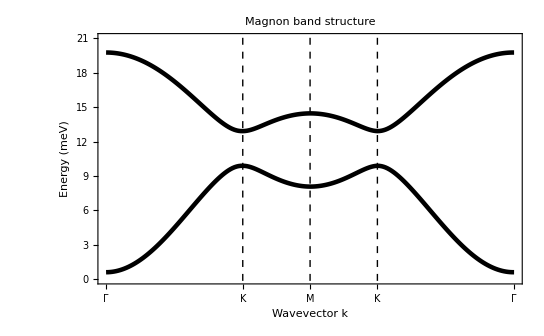

```mathematica
J=k=Γ=dSIA=dDM=J2=J3=H=0;

(*======================================= INPUTS =======================================*)

(*================== k-space path ==================*)
(*K–Γ–M–K*)
(*path={"K","Γ","M","K"};*)

(*Γ–M–K–Γ*)
(*path={"Γ","M","K","Γ"};*)

(*Γ–M–Γ–M–Γ*)
(*path={"Γ","M","Γ","M","Γ"};*)

(*M–K–Γ–K–M*)
(*path={"M","K","Γ","K","M"};*)

(*Γ–K–M–K–Γ*)
path={"Γ","K","M","K","Γ"};
(*===================================================*)

(*==========================================================================*)
(*==================== Coupling constants (units: meV) ====================*)
(*==========================================================================*)

(* ========== JKG/JK+SIA model ========== *)

(*Heisenberg coupling*)
J=-3;
(*Kitaev coupling*)
k=-5;
(*Symmetric off-diagonal (Gamma) coupling*)
Γ=-0.1;
(*Second- and third-nearest-neighbor Heisenberg coupling*)
J2=0;
J3=0;
(*DM interaction coupling*)
dDM=0;
(*Single-ion anisotropy*)
dSIA=0;
(*External magnetic field (warning: units are not meV)*)
H=0;

(* ====================================== *)

(*==========================================================================*)
(*==========================================================================*)
(*==========================================================================*)

(*Minimum and maximum energies to plot on the y-axis*)
ymin=0;
ymax=21;
(*ymin=0;
ymax=Automatic;*)

(*Appearance of the lines that plot the magnon bands*)
bandLinesStyle={Thickness[0.006],Black(*Red*)(*,Opacity[0]*)};

(*Appearance of the vertical lines that mark where the high symmetry points are*)
highSymmetryPointsVerticalLinesStyle={Black,Dashed};

(*Axis labels*)
yaxisLabelLeft="Energy (meV)";
(*yaxisLabelLeft="Energy / |J|";*)
xaxisLabelBottom="Wavevector k";
yaxisLabelRight=None;
xaxisLabelTop=None;

(*=======================================================================================*)

Γgap=Abs[Min[eigenvals[Γpoint]]];
Kgap=Abs[Differences[eigenvals[Kpoint]][[1]]];

Print["Γ point gap = ",Round[Γgap,0.01]," meV"];
Print["K point gap = ",Round[Kgap,0.01]," meV"];

plotSizeScalingFactor=1;

plotMagnonBandStructure[path,ymin,ymax,bandLinesStyle,highSymmetryPointsVerticalLinesStyle,yaxisLabelLeft,xaxisLabelBottom,yaxisLabelRight,xaxisLabelTop,imageSize={544,380}plotSizeScalingFactor,numSteps=200]
```

## Path in k-space

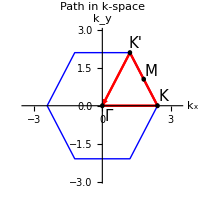

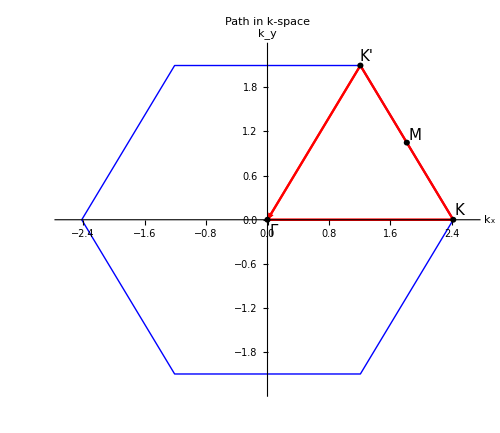

```mathematica
(*Γ–M–K–Γ*)
path={"Γ","M","K","Γ"};
path={"Γ","K","M","K'","Γ"};

plotkspacePathSmall[path]
plotkspacePathLarge[path]
```

## Density of states

runtime = 8.59518 s

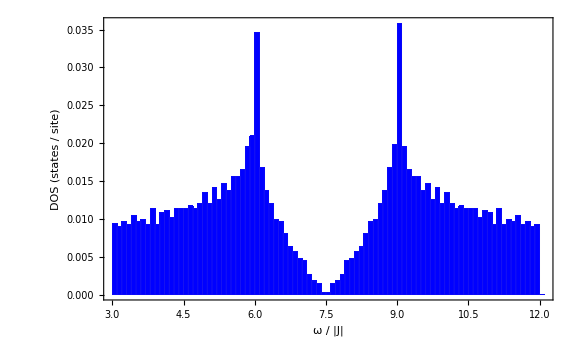

```mathematica
numkvecsProbedAlongADirection=100;

time=AbsoluteTiming[
energyvalsProbed=probeEnergyvalsInFirstBrillouinZone[numkvecsProbedAlongADirection]
][[1]];
Print["runtime = "<>ToString[time]<>" s"];

numBins=100;
(*xlabel="Energy / site (meV)";*)
(*xlabel="Energy / site (J)";*)
(*xlabel="ω / |J| per site";*)
xlabel="ω / |J|";
ylabel="DOS (states / site)";
plotOptions={Frame->{True,True,False,False},FrameStyle->Directive[Black,16],LabelStyle->Directive[Black,16],ImageSize->Large,ChartStyle->{(*Red,*)(*Orange,*)(*Green*)(*,*)Blue},FrameLabel->{xlabel,ylabel}};

(*Plot*)
Histogram[energyvalsProbed,numBins,(#2/(2numkvecsProbedTotal))&,Evaluate[plotOptions]]
```

## Magnetization

runtime = 2.27241 s

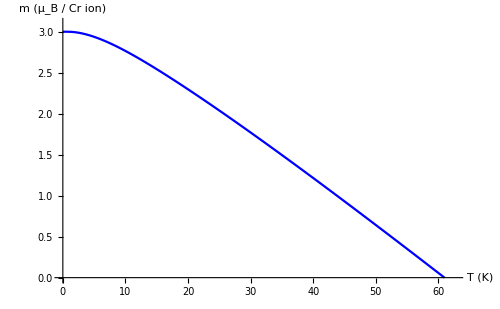

```mathematica
minT=0.01;
maxT=62;
numTvals=100;
couplingConstantUnits="meV";
(*couplingConstantUnits="K";*)
numkvecsProbedAlongADirection=50;

time=AbsoluteTiming[
mag=magnetization[minT,maxT,numTvals,couplingConstantUnits,numkvecsProbedAlongADirection];
][[1]];
Print["runtime = "<>ToString[time]<>" s"];

(*Convert magnetization units to μB / site*)
mag[[All,2]]*=2;

(*Axis labels*)
xlabel="T (K)";
(*xlabel="T / |J|";*)
(*ylabel="m_e_3";*)
ylabel="m (μ_B / Cr ion)";

ListLinePlot[mag,PlotRange->{{0,1.01maxT},{0,3.1}},AxesLabel->{Style[xlabel],Style[ylabel]},LabelStyle->Directive[16,Black],AxesStyle->Directive[16,Black],PlotStyle->Directive[16,Blue],ImageSize->500]
```

## Susceptibility

runtime = 4.08917 s

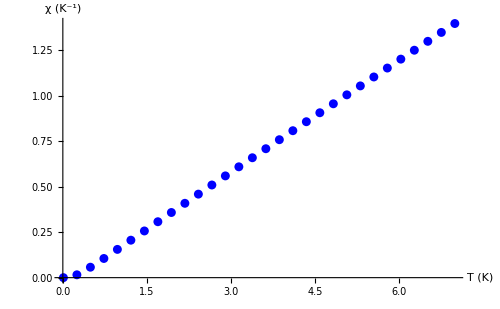

```mathematica
minT=0.01;
maxT=7;
numTvals=30;
(*couplingConstantUnits="meV";*)
couplingConstantUnits="K";
numkvecsProbedAlongADirection=50;

time=AbsoluteTiming[
susc=susceptibility[minT,maxT,numTvals,couplingConstantUnits,numkvecsProbedAlongADirection];
][[1]];
Print["runtime = "<>ToString[time]<>" s"];

(*Axis labels*)
xlabel="T (K)";
(*xlabel="T / |J|";*)
ylabel="χ (K^-1)";

ListPlot[susc,(*PlotRange->{{0,100},{0,3.5}},*)AxesLabel->{Style[xlabel],Style[ylabel]},LabelStyle->Directive[16,Black],AxesStyle->Directive[16,Black],PlotStyle->Directive[16,Blue],ImageSize->500]
```